```mathematica
SetDirectory["C:\Users\Ivan\Documents\INP_VEPP4M\INP_VEPP4M_betaFuctions"];
```

```mathematica
{name, first} = Transpose[Import["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\name.dat", "Table"]] ;
name
first
```

{stp0,stp2,stp4,srp1,srp2,srp3,srp4,srp5,srp6,srp7,srp8,srp9,sip1,sip2,srp10,srp11,srp12,srp13,srp14,srp15,srp16,srp17,sep5,sep4,sep3,sep1,sep0,nep0,nep1,nep3,nep4,nep5,nrp17,nrp16,nrp15,nrp14,nrp13,nrp12,nrp11,nrp10,nip3,nip1,nrp9,nrp8,nrp7,nrp6,nrp5,nrp4,nrp3,nrp2,nrp1,ntp4,ntp2,ntp0}

{9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
k=IntegerString[#, 10, 2] & /@ Range[10]
```

{01,02,03,04,05,06,07,08,09,10}

```mathematica
(* Load experiment data *)
ClearAll[load] ;
load[id_] := Block[
	{prefix},
	prefix = StringTemplate["C:\\Users\\Ivan\\Documents\\Учеба\\Диплом\\Данные\\`1`-n450-2000-10000-"][IntegerString[id, 10, 2]] ;
	Table[
		Take[N[Import[StringTemplate["`1``2`.dat"][prefix, name[[i]]], "CSV"]], {first[[i]]+1, first[[i]]+1 + 1023}],
		{i, 1, 54}
	]
] ;
dataExp = Table[load[i],{i,1,10}] ;
```

```mathematica
lenDat=10;
```

```mathematica
(*Beta from phase+(Ampl,Phase,Freq)*)
APF=Table[signalProc[dataExp[[i]],1,128],{i,1,lenDat}];
ClearAll[BFP];
BFP[bpm$bx_,bpm$fx_]:=Block[
{BFPX,DataBFPX,DataBFPX$StandartDeviation,BetaBPMs},
BFPX=Table[betaFromPhase[APF[[i]],bpm$bx,bpm$fx],{i,1,lenDat}];
DataBFPX=Table[BFPX[[i]][[j]],{j,1,54},{i,1,lenDat}];
BetaBPMs=Table[Mean[DataBFPX[[i]]],{i,1,54}];
DataBFPX$StandartDeviation=Table[Around [Mean[DataBFPX[[i]]], StandardDeviation[DataBFPX[[i]]]],{i,1,54}];
{DataBFPX$StandartDeviation,BetaBPMs}
]
```

```mathematica
(*Beta from Ampl*)
ClearAll[BFA];
BFA[bpm$bx_]:=Block[
{BFAX,DataBFAX,DataBFAX$StandartDeviation,BetaBPMs},
BFAX=Table[Insert[betaFromAmpl[Drop[APF[[i]],{10,10}],Drop[bpm$bx,{10,10}]],"non",10],{i,1,lenDat}];
DataBFAX=Table[BFAX[[i]][[j]],{j,1,54},{i,1,lenDat}];
BetaBPMs=Table[Mean[DataBFAX[[i]]],{i,1,54}];
DataBFAX$StandartDeviation=Table[Around [Mean[DataBFAX[[i]]], StandardDeviation[DataBFAX[[i]]]],{i,1,54}];
{DataBFAX$StandartDeviation,BetaBPMs}
]
```

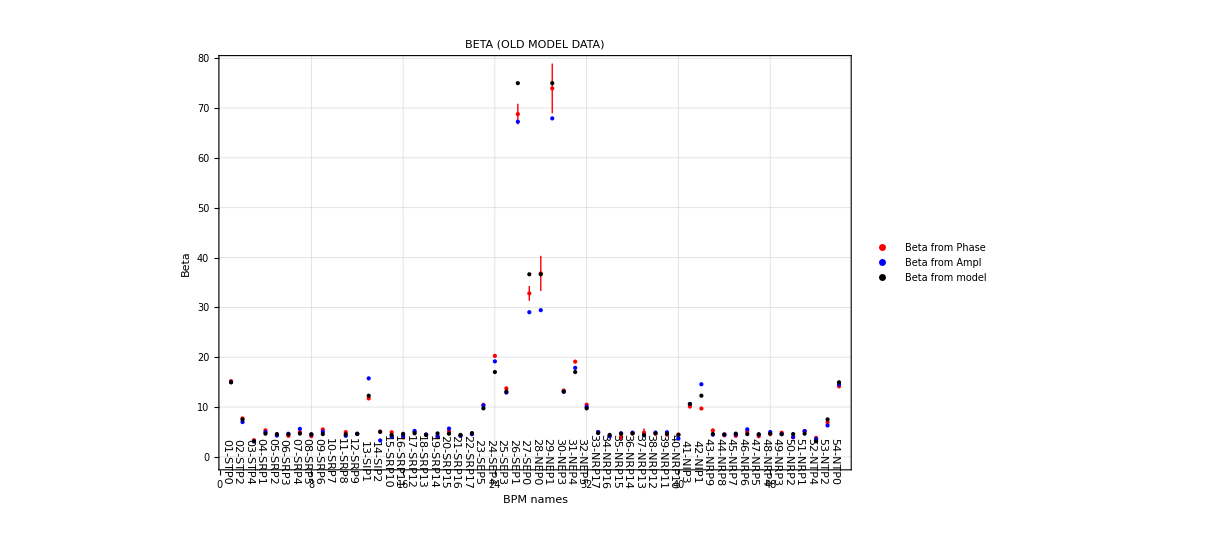
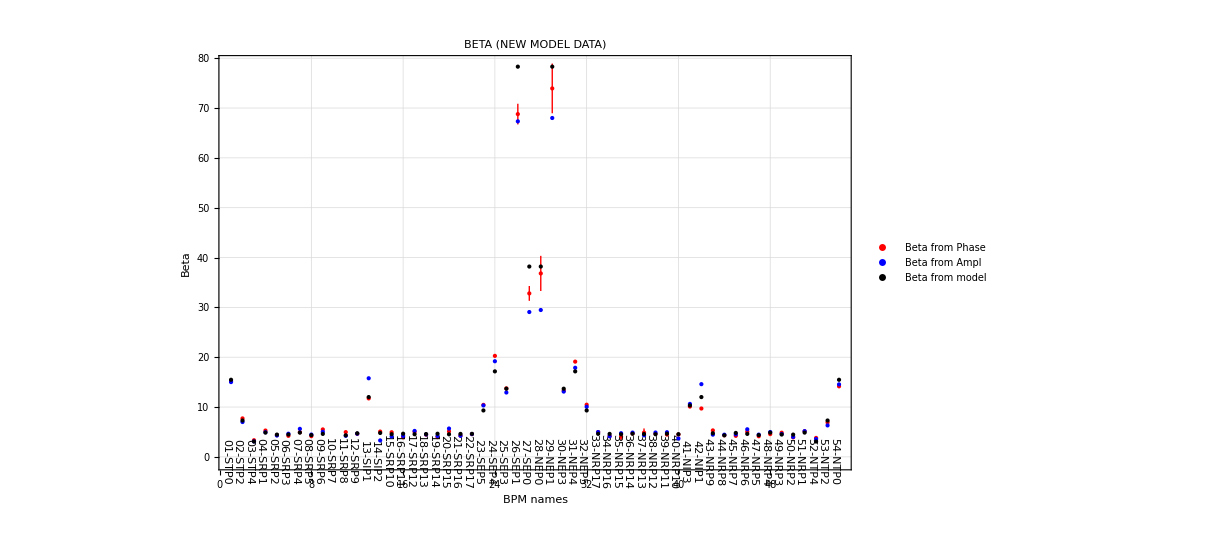
-Graphics- | -Graphics-

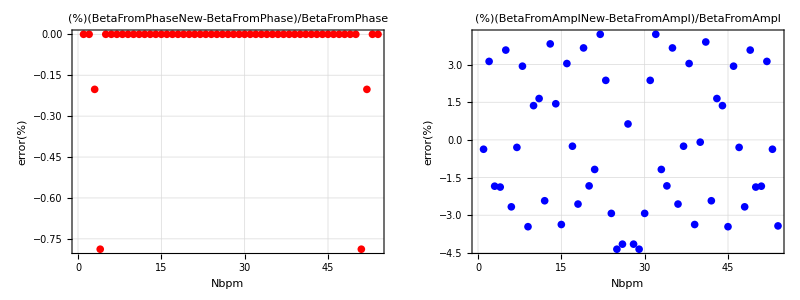

{15.4724,7.29783,3.07917,4.8699,4.46947,4.4822,4.86662,4.37045,4.61,4.80492,4.32025,4.73484,11.9994,4.79456,4.55338,4.65056,4.54462,4.58067,4.64127,4.52901,4.60959,4.62052,9.31418,17.1551,13.6791,78.3005,38.1915,38.1915,78.3005,13.6791,17.1551,9.31418,4.62052,4.60959,4.52901,4.64127,4.58067,4.54462,4.65056,4.55338,10.3191,11.9994,4.73484,4.32025,4.80492,4.61,4.37045,4.86662,4.4822,4.46947,4.8699,3.07917,7.29783,15.4724}

{14.9658,7.51225,3.13265,4.65642,4.57645,4.53559,4.66694,4.54261,4.56762,4.6605,4.51869,4.60414,12.2789,5.01504,4.41905,4.62236,4.72729,4.39202,4.70872,4.64572,4.40825,4.76988,9.73702,17.0228,13.0875,74.984,36.6399,36.6399,74.984,13.0875,17.0228,9.73702,4.76988,4.40825,4.64572,4.70872,4.39202,4.72729,4.62236,4.41905,10.617,12.2789,4.60414,4.51869,4.6605,4.56762,4.54261,4.66694,4.53559,4.57645,4.65642,3.13265,7.51225,14.9658}

-Graphics-

Part::partd: Part specification {1.91635,1.65167,0.459912}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {1.91635,1.65167,0.459912}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {1.91635,1.65167,0.459912}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {1.91635,1.65167,0.459912} does not exist.

Part::partw: Part 5 of {1.91635,1.65167,0.459912} does not exist.

Part::partw: Part 4 of {1.91635,1.65167,0.459912} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
PlotBFF=Show[ListPlot[BFP[bpm$bx,bpm$fx][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Red],IntervalMarkersStyle->Red,PlotLegends->{"Beta from Phase"},PlotTheme->"Detailed"]];
PlotBFA=Show[ListPlot[BFA[bpm$bx][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Blue],IntervalMarkersStyle->Blue,PlotLegends->{"Beta from Ampl"},PlotTheme->"Detailed"]];
PlotBFFN=Show[ListPlot[BFP[bpm$bxN,bpm$fxN][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Red],IntervalMarkersStyle->Red,PlotLegends->{"Beta from Phase"},PlotTheme->"Detailed"]];
PlotBFAN=Show[ListPlot[BFA[bpm$bxN][[1]],PlotRange->All,PlotStyle->Directive[PointSize[Medium],Blue],IntervalMarkersStyle->Blue,PlotLegends->{"Beta from Ampl"},PlotTheme->"Detailed"]];
{
plot$beta = Show[
	PlotBFF,
PlotBFA,
plot$bpm ,
plotBetaModelX,
PlotRange->{All, {-10, All}},PlotLabel->"BETA (OLD MODEL DATA)",FrameLabel->{"BPM names", "Beta"},
	ImageSize -> 900
] ,
plot$betaN = Show[
	PlotBFFN,
PlotBFAN,
plot$bpm ,
plotBetaModelXN,
PlotRange->{All, {-10, All}},PlotLabel->"BETA (NEW MODEL DATA)",FrameLabel->{"BPM names", "Beta"},
	ImageSize -> 900
] }//List//Grid
deltBP=(BFP[bpm$bxN,bpm$fxN][[2]]-BFP[bpm$bx,bpm$fx][[2]])/BFP[bpm$bx,bpm$fx][[2]]*100;
deltBA=(BFA[bpm$bxN,bpm$fxN][[2]]-BFA[bpm$bx,bpm$fx][[2]])/BFA[bpm$bx,bpm$fx][[2]]*100;
{
ListPlot[deltBP,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",PlotLabel->"(%)(BetaFromPhaseNew-BetaFromPhase)/BetaFromPhase", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}],
ListPlot[deltBA,PlotRange->All,PlotStyle->Blue,PlotTheme->"Detailed",PlotLabel->"(%)(BetaFromAmplNew-BetaFromAmpl)/BetaFromAmpl", AspectRatio->1/2, ImageSize->500, FrameLabel->{"Nbpm", "error(%)"}]
}//List//Grid
bpm$bxN 
bpm$bx
```